## Plot of Bootstrapped EWS for Ricker undergoing Fold

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_bootstrap/model_ricker"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,30,10,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
bl=0;
bh=3; (* realisation nuber for individual trajectory and power spectrum evolution *)
rw=0.25; (* rolling window *)
```

## Import Data

```mathematica
ewsStd=Import["data_export/sim1_ews.csv"];
ewsBoot=Import["data_export/sim1_ews_boot.csv"];
```

```mathematica
ewsBoot[[1]]
```

{,Quantile,Time,State variable,Smoothing,Residuals,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,AIC fold,AIC hopf,AIC null,Smax,Smax/Var}

```mathematica
ewsBoot[[2;;,{2,11}]]
```

{{0.05,0.032853},{0.05,0.246677},{0.05,0.0226704},{0.05,0.00441899},{0.05,0.0844519},{0.05,0.0262057},{0.05,0.0251617},{0.05,0.00433699},{0.05,0.01119},{0.05,0.00475665},{0.05,0.135432},{0.05,0.0145069},{0.05,0.00017903},{0.05,0.000159889},{0.05,0.000951624},{0.05,0.0000806678},{0.05,0.000245384},{0.05,0.0361972},{0.05,0.0159028},{0.05,0.0294545},{0.05,0.00588143},{0.05,0.0002517},{0.05,0.0000111296},{0.05,0.00248888},{0.05,0.0000598443},{0.05,0.0000264132},{0.05,4.92906×10^-7},{0.05,0.0000171785},{0.05,2.3818×10^-6},{0.05,2.76239×10^-8},{0.05,0.000158008},{0.05,0.0203171},{0.05,0.0000632741},{0.05,1.45829×10^-6},{0.05,0.000032819},{0.05,0.000912797},{0.05,0.00027757},{0.05,0.000127086},{0.05,2.67898×10^-10},{0.05,2.36932×10^-7},{0.05,1.06184×10^-7},{0.05,9.91054×10^-11},{0.05,4.15292×10^-9},{0.05,2.80001×10^-13},{0.05,3.17893×10^-12},{0.05,6.43007×10^-10},{0.05,3.18854×10^-11},{0.05,1.02573×10^-11},{0.05,4.80882×10^-12},{0.05,3.03022×10^-11},{0.05,1.32842×10^-13},{0.05,7.95225×10^-11},{0.05,9.40908×10^-14},{0.05,6.58902×10^-13},{0.05,9.31263×10^-14},{0.25,0.942552},{0.25,0.851273},{0.25,0.86296},{0.25,0.664266},{0.25,0.904453},{0.25,0.919427},{0.25,0.902818},{0.25,0.947041},{0.25,0.953603},{0.25,0.878731},{0.25,0.958741},{0.25,0.859845},{0.25,0.756345},{0.25,0.857249},{0.25,0.785728},{0.25,0.86955},{0.25,0.816225},{0.25,0.955686},{0.25,0.825396},{0.25,0.823353},{0.25,0.874066},{0.25,0.766724},{0.25,0.351831},{0.25,0.77786},{0.25,0.291516},{0.25,0.429806},{0.25,0.0306828},{0.25,0.38715},{0.25,0.0780778},{0.25,0.00048285},{0.25,0.687126},{0.25,0.888266},{0.25,0.808128},{0.25,0.330332},{0.25,0.659784},{0.25,0.951351},{0.25,0.955093},{0.25,0.845052},{0.25,0.0017158},{0.25,0.00365142},{0.25,0.0267524},{0.25,0.000623502},{0.25,0.0000222648},{0.25,2.80686×10^-7},{0.25,0.000198388},{0.25,0.000123121},{0.25,0.000272375},{0.25,5.16085×10^-6},{0.25,0.0000379296},{0.25,0.000116404},{0.25,0.0000363748},{0.25,0.00705905},{0.25,3.56223×10^-6},{0.25,8.00521×10^-6},{0.25,3.53282×10^-8},{0.5,0.983193},{0.5,0.971369},{0.5,0.969115},{0.5,0.974518},{0.5,0.983663},{0.5,0.995881},{0.5,0.995332},{0.5,0.991912},{0.5,0.990109},{0.5,0.988171},{0.5,0.991278},{0.5,0.990653},{0.5,0.976796},{0.5,0.982889},{0.5,0.98923},{0.5,0.989033},{0.5,0.984093},{0.5,0.988015},{0.5,0.978339},{0.5,0.977161},{0.5,0.981971},{0.5,0.979069},{0.5,0.957356},{0.5,0.973551},{0.5,0.971505},{0.5,0.940897},{0.5,0.966598},{0.5,0.981322},{0.5,0.970494},{0.5,0.896921},{0.5,0.990764},{0.5,0.991226},{0.5,0.989275},{0.5,0.989839},{0.5,0.994256},{0.5,0.99868},{0.5,0.997308},{0.5,0.998137},{0.5,0.855279},{0.5,0.969587},{0.5,0.852383},{0.5,0.825788},{0.5,0.244009},{0.5,0.00380775},{0.5,0.316276},{0.5,0.601051},{0.5,0.688259},{0.5,0.0113088},{0.5,0.410213},{0.5,0.525172},{0.5,0.338452},{0.5,0.701669},{0.5,0.337869},{0.5,0.572316},{0.5,0.00189173},{0.75,0.995732},{0.75,0.995143},{0.75,0.991383},{0.75,0.994154},{0.75,0.996811},{0.75,0.999264},{0.75,0.999403},{0.75,0.99796},{0.75,0.998359},{0.75,0.99859},{0.75,0.999334},{0.75,0.998852},{0.75,0.996906},{0.75,0.996952},{0.75,0.998826},{0.75,0.998849},{0.75,0.998341},{0.75,0.998108},{0.75,0.997067},{0.75,0.993927},{0.75,0.996762},{0.75,0.997943},{0.75,0.992961},{0.75,0.993668},{0.75,0.99662},{0.75,0.994033},{0.75,0.996856},{0.75,0.996731},{0.75,0.999456},{0.75,0.998177},{0.75,0.999037},{0.75,0.99955},{0.75,0.999689},{0.75,0.999517},{0.75,0.999873},{0.75,0.999854},{0.75,0.999756},{0.75,0.999945},{0.75,0.998935},{0.75,0.999777},{0.75,0.999601},{0.75,0.999251},{0.75,0.995557},{0.75,0.994213},{0.75,0.999939},{0.75,0.99996},{0.75,0.999704},{0.75,0.9833},{0.75,0.999697},{0.75,0.999975},{0.75,0.999929},{0.75,0.999716},{0.75,0.99988},{0.75,0.999049},{0.75,0.997258},{0.95,0.999874},{0.95,0.99946},{0.95,0.998608},{0.95,0.998948},{0.95,0.999864},{0.95,0.999887},{0.95,0.999955},{0.95,0.999828},{0.95,0.99996},{0.95,0.999958},{0.95,0.999973},{0.95,0.999943},{0.95,0.999751},{0.95,0.999665},{0.95,0.999913},{0.95,0.999925},{0.95,0.99986},{0.95,0.99992},{0.95,0.999748},{0.95,0.99968},{0.95,0.999891},{0.95,0.999899},{0.95,0.999067},{0.95,0.999877},{0.95,0.99988},{0.95,0.999504},{0.95,0.999787},{0.95,0.999929},{0.95,0.999963},{0.95,0.999978},{0.95,0.99995},{0.95,0.999991},{0.95,0.999993},{0.95,0.999987},{0.95,0.999998},{0.95,0.999997},{0.95,0.999995},{0.95,0.999998},{0.95,0.999984},{0.95,0.999998},{0.95,0.999997},{0.95,0.999994},{0.95,0.999998},{0.95,0.999999},{0.95,1.},{0.95,1.},{0.95,1.},{0.95,0.999999},{0.95,1.},{0.95,1.},{0.95,1.},{0.95,0.999999},{0.95,1.},{0.95,1.},{0.95,1.}}

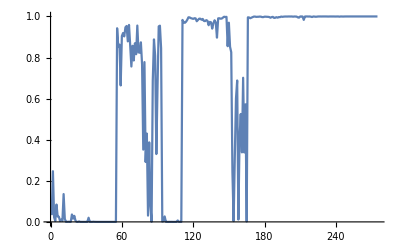

```mathematica
ListLinePlot[ewsBoot[[2;;,11]]]
```

## Trajectory Plots

```mathematica
ewsStd[[1]]
```

{,Time,State variable,Smoothing,Residuals,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,AIC fold,AIC hopf,AIC null,Params fold,Params hopf,Params null,Smax,Smax/Var}

```mathematica
(* Extract info *)
tVals = ewsStd[[2;;,2]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
xVals = ewsStd[[2;;,3]];
```

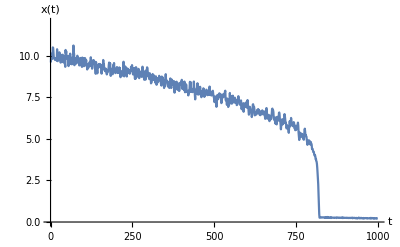

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[xVals,
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},{0,12}}]
```

## Bifurcation Diagram (exploited pop)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
(* Import data *)
rawdata=Import["../../fisheries/bifurcation/fish_exp.dat"];

(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of F *)
fbifVals=fulldata[[;;,1]];
tbifVals=(fbifVals-bl)*tmax /(bh-bl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
(*nodeSections[[3]]=Cases[nodeSections[[3]],{x_,_,_,_}/; x>0] ; 
nodeSections=Append[nodeSections,Cases[nodeSections[[6]],{_,x_,_,_}/;x>0]];
nodeSections[[6]]=Cases[nodeSections[[6]],{_,x_,_,_}/;x<0]; *)(* had to seperate out branches for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1}

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

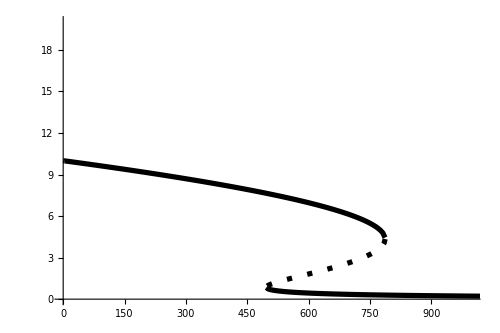

```mathematica
(* Make plot *)
bifPlotExp=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

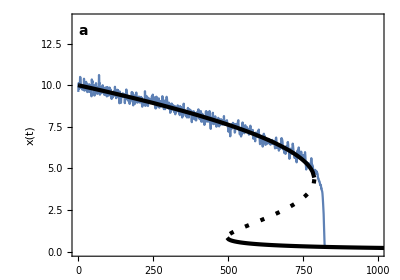

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajX=Show[{plotX,bifPlotExp},
PlotRange->{{0,tmax},{0,14}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
AspectRatio->0.7,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
]
```

## EWS Plots

### Variance

```mathematica
indexStd=Position[ewsStd[[1]],"Variance"][[1,1]];
indexBoot = Position[ewsBoot[[1]],"Variance"][[1,1]];
```

```mathematica
ewsBoot[[1]]
```

{,Quantile,Time,State variable,Smoothing,Residuals,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,AIC fold,AIC hopf,AIC null,Smax,Smax/Var}

```mathematica
Flatten[Position[ewsBoot[[;;,2]],0.05]]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

```mathematica
(* Extract quantile information *)
quant0p05=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.05]]]][[;;,{3,indexBoot}]];
quant0p25=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.25]]]][[;;,{3,indexBoot}]];
quant0p5=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.5]]]][[;;,{3,indexBoot}]];
quant0p75=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.75]]]][[;;,{3,indexBoot}]];
quant0p95=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.95]]]][[;;,{3,indexBoot}]];
```

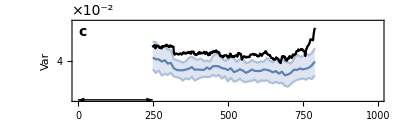

```mathematica
(* Plot bootstrapped and standard EWS *)
ymin=0.02;
ymax=0.06;
plotVar=ListLinePlot[{quant0p5,quant0p05,quant0p95,ewsStd[[2;;,{1,indexStd}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{1->{2},1->{3}}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],Black},
FrameLabel->{{"Var",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Transpose[{Range[0,10,2]*10^(-2),Range[0,10,2]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight},{windowComps*dt2,ymin}]}],
Text[Style["×10^-2",14],indexPos],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation combined

```mathematica
list={1,2,3,4};
```

```mathematica
Position[list,#][[1,1]]&/@{2,3}
```

{2,3}

```mathematica
indexStd=Position[ewsStd[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
indexBoot = Position[ewsBoot[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
Join
```

Join

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,3}]],Table["τ="<>ToString[i],{i,{1,2}}],Spacings->{0,0.1}]
```

```mathematica
(* Extract quantile information *)
quant0p05=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.05]]]][[;;,Prepend[indexBoot,3]]];
quant0p25=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.25]]]][[;;,Prepend[indexBoot,3]]];
quant0p5=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.5]]]][[;;,Prepend[indexBoot,3]]];
quant0p75=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.75]]]][[;;,Prepend[indexBoot,3]]];
quant0p95=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.95]]]][[;;,Prepend[indexBoot,3]]];
```

```mathematica
ewsStd[[1]]
```

{,Time,State variable,Smoothing,Residuals,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,AIC fold,AIC hopf,AIC null,Params fold,Params hopf,Params null,Smax,Smax/Var}

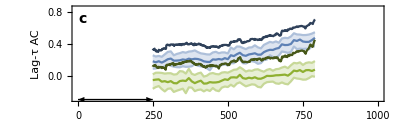

```mathematica
ymin=-0.3;
ymax=0.85;
plotAC=ListLinePlot[{quant0p5[[;;,{1,2}]],quant0p05[[;;,{1,2}]],quant0p95[[;;,{1,2}]],ewsStd[[2;;,{1,indexStd[[1]]}]],
quant0p5[[;;,{1,3}]],quant0p05[[;;,{1,3}]],quant0p95[[;;,{1,3}]],ewsStd[[2;;,{1,indexStd[[2]]}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{1->{2},1->{3},5->{6},5->{7}}},
FrameLabel->{{"Lag-τ AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],Darker[TMBcolours⟦1⟧,0.5],
TMBcolours⟦3⟧,Lighter[TMBcolours⟦3⟧,0.5],Lighter[TMBcolours⟦3⟧,0.5],Darker[TMBcolours⟦3⟧,0.5]},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Smax

```mathematica
indexStd=Position[ewsStd[[1]],"Smax"][[1,1]];
indexBoot = Position[ewsBoot[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract quantile information *)
quant0p05=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.05]]]][[;;,{3,indexBoot}]];
quant0p25=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.25]]]][[;;,{3,indexBoot}]];
quant0p5=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.5]]]][[;;,{3,indexBoot}]];
quant0p75=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.75]]]][[;;,{3,indexBoot}]];
quant0p95=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.95]]]][[;;,{3,indexBoot}]];
```

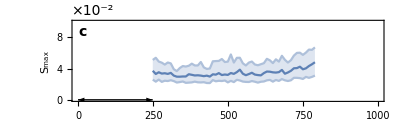

```mathematica
(* Plot bootstrapped and standard EWS *)
ymin=0;
ymax=0.01;
plotSmax=ListLinePlot[{quant0p5,quant0p05,quant0p95,ewsStd[[2;;,{1,indexStd}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{1->{2},1->{3}}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],Black},
FrameLabel->{{"S_max",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Transpose[{Range[0,10,2]*10^(-3),Range[0,10,2]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight},{windowComps*dt2,ymin}]}],
Text[Style["×10^-2",14],indexPos],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### AIC

```mathematica
indexStd=Position[ewsStd[[1]],#][[1,1]]&/@{"AIC fold","AIC hopf", "AIC null"};
indexBoot = Position[ewsBoot[[1]],#][[1,1]]&/@{"AIC fold","AIC hopf", "AIC null"};
```

```mathematica
indexStd
```

{10,11,12}

```mathematica
(* Extract quantile information *)
quant0p05=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.05]]]][[;;,Prepend[indexBoot,3]]];
quant0p25=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.25]]]][[;;,Prepend[indexBoot,3]]];
quant0p5=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.5]]]][[;;,Prepend[indexBoot,3]]];
quant0p75=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.75]]]][[;;,Prepend[indexBoot,3]]];
quant0p95=ewsBoot[[Flatten[Position[ewsBoot[[;;,2]],0.95]]]][[;;,Prepend[indexBoot,3]]];
```

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,3,4}]],{"ω_fold","ω_hopf","ω_null"},Spacings->{0,0.1}]
```

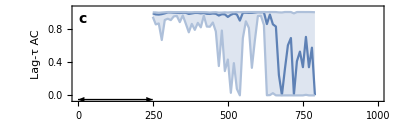

```mathematica
ymin=-0.05;
ymax=1.05;
plotAIC=ListLinePlot[{quant0p5[[;;,{1,2}]],quant0p25[[;;,{1,2}]],quant0p75[[;;,{1,2}]],ewsStd[[2;;,{1,indexStd[[1]]}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{1->{2},1->{3},5->{6},5->{7}}},
FrameLabel->{{"Lag-τ AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],Darker[TMBcolours⟦1⟧,0.5],
TMBcolours⟦3⟧,Lighter[TMBcolours⟦3⟧,0.5],Lighter[TMBcolours⟦3⟧,0.5],Darker[TMBcolours⟦3⟧,0.5]},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

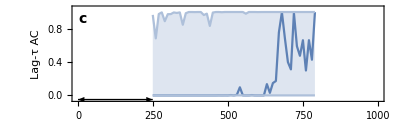

```mathematica
ymin=-0.05;
ymax=1.05;
plotAIC=ListLinePlot[{quant0p5[[;;,{1,3}]],quant0p05[[;;,{1,3}]],quant0p95[[;;,{1,3}]],ewsStd[[2;;,{1,indexStd[[2]]}]]},
Joined->True,
LabelStyle->14,
Frame->True,
Filling->{{1->{2},1->{3},5->{6},5->{7}}},
FrameLabel->{{"Lag-τ AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{ymin,ymax}},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],Darker[TMBcolours⟦1⟧,0.5],
TMBcolours⟦3⟧,Lighter[TMBcolours⟦3⟧,0.5],Lighter[TMBcolours⟦3⟧,0.5],Darker[TMBcolours⟦3⟧,0.5]},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.72}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Power Spectrum

```mathematica
specData//Dimensions
```

{}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[2;;,3]]]
```

Part::take: Cannot take positions 2 through -1 in specData.

Part::pkspec1: The expression specData cannot be used as a part specification.

3⟦specData,2;;All⟧

```mathematica
pspecs=Table[
Cases[specData,
{relNum,"x",i,_,_}]⟦;;,{4,5}⟧,
{i,plotTimes}];
```

Table::iterb: Iterator {i,3⟦specData,2;;All⟧} does not have appropriate bounds.

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

Part::take: Cannot take positions 2 through -1 in 3.

BarLegend[{TemperatureMap,3⟦2;;All⟧},LegendLabel→Time,LegendMarkerSize→150]

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
plotPspec=ListLinePlot[pspecs,
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{2*padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-2",14],Scaled[{0.065,1.05}]],
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
FrameTicks->{{Transpose[{Range[0,20,2]*10^(-2),Range[0,20,2]}],None},{Automatic,None}},
PlotLegends->Placed[colLegend,Scaled[{0.91,0.58}]]]
```

Table::iterb: Iterator {i,3.⟦specData,2;;All⟧} does not have appropriate bounds.

Part::pkspec1: The expression specData cannot be used as a part specification.

Table::iterb: Iterator {i,3.⟦specData,2;;All⟧} does not have appropriate bounds.

ListLinePlot::lpn: Table[Cases[specData,{relNum,x,i,_,_}]⟦1;;All,{4,5}⟧,{i,3.⟦specData,2;;All⟧}] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression specData cannot be used as a part specification.

Table::iterb: Iterator {i,3.⟦specData,2;;All⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Table[Cases[specData,{relNum,x,i,_,_}]⟦1;;All,{4,5}⟧,{i,3.⟦specData,2;;All⟧}] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression specData cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: Table[Cases[specData,{relNum,x,i,_,_}]⟦1;;All,{4,5}⟧,{i,3.⟦specData,2;;All⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Table[Cases[specData,{relNum,x,i,_,_}]⟦1;;All,{4,5}⟧,{i,3⟦specData,2;;All⟧}],PlotRange→All,PlotStyle→{Blend[TemperatureMap,-3+3⟦specData,2;;All⟧] Blend[TemperatureMap,1/(-3+2;;All)]},LabelStyle→13,Frame→True,AxesOrigin→{0,0},ImagePadding→{{60,30},{20,20}},ImageSize→400,AspectRatio→0.7,FrameLabel→{{S(ω),None},{None,None}},PlotRangeClipping→False,Epilog→{Text[×10^-2,Scaled[{0.065,1.05}]],Text[d,Scaled[{0.035,0.93}]],Text[ω,Scaled[{1.05,0}]]},FrameTicks→{{{{0,0},{1/50,2},{1/25,4},{3/50,6},{2/25,8},{1/10,10},{3/25,12},{7/50,14},{4/25,16},{9/50,18},{1/5,20}},None},{Automatic,None}},PlotLegends→Placed[BarLegend[{TemperatureMap,3⟦2;;All⟧},LegendLabel→Time,LegendMarkerSize→150],Scaled[{0.91,0.58}]]]

## Grid: Single EWS

```mathematica
gridPlot=Grid[{{bifTrajX,""},{plotVar,plotSmax},{plotAC,plotAIC},{},{}},Spacings->{-1.5,0}]
```

-Graphics- | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-
 | 
 |

```mathematica
(*Export["figures/plot_ews_fold.png",gridPlot,ImageResolution->200];*)
```